```mathematica
(* +----------------------------------- test_db -------------------------------------+ *)
(* +                                                                                + *)
(* +           test_db is a consistency check to evaluate the database match, i.e.   + *)
(* +           the match of a given coordination with the database rotation variants + *)
(* +           test_db creates a temperature map for the match of a selected database     + *)
(* +           item against all database items.                                      + *)
(* +           The "lower" the temperature in the map the better the match.           + *)
(* +           It also creates a plot of the best matching database item against     + *)
(* +           the test item. Both should be identical.                              + *)
(* +                                                                                + *) 
(* +           INPUT:  Database file, created with create_db                        + *)
(* +                   Index of the test item                                       + *)
(* +           OUTPUT: Temperature map that shows the distance norm between the      + *)         
(* +                   database coordination and the coordination of test item     + *)
(* +                   The output is displayed in the script file.                  + *)
(* +           USAGE:  (1) Delete All Output (from the 'Cell' menu)                  + *)
(* +                   (2) Fill the section between 'BEGIN USER INPUT' and           + *)
(* +                      'END USER INPUT'                                           + *)
(* +                   (3) Evaluate Notebook (from the'Evaluate' menu)              + *)
(* +           DEPENDENCIES: None                                                  + *)
(* +                                                                                + *)
(* +           AUTHOR:  L. Houben, Weizmann Institute of Science                    + *)
(* +                    lothar.houben(at)weizmann.ac.il                             + *)
(* +           COPYRIGHT: This software is licensed under the GNU GENERAL PUBLIC    + *)
(* +                      LICENSE Version 3                                         + *)
(* +----------------------------------------------------------------------------------+ *)
(* +-------------------------- BEGIN USER INPUT --------------------------------------+ *)                                                                         
(* +-----------------------------------------------------------------------------------+ *)
(* baseDir is the base folder for program input and output.                            *)                        
(* dbDir is a subfolder that holds the database file.                                   *)
(* Please make sure that the folders exist.                                           *)
baseDir=StringJoin[$HomeDirectory,"/Desktop/OrderParameterAnalysis"];   
dbDir ="db";
(* dbfileName is name of the database file                  *)
dbfileName="rotation-database_Fcc_50_1.db";
(* testitem is the index of the database to test against the database                 *)
testitem=1;
(* +---------------------------------------------------------------------------------  + *)
(* +-------------------------- END-- USER INPUT --------------------------------------+ *)                                                                         
(* +---------------------------------------------------------------------------------- + *)
```

```mathematica
(* Load the database file and the datafile *) 
DBfile= StringJoin[baseDir,"/",dbDir,"/",dbfileName];
ModelDB=.;
ModelDB=Get[DBfile];
coordination=Length[ModelDB[[1,3]]];
NDBItems=Length[ModelDB[[All,1]]];
```

```mathematica
(* QuickDistance is a module that calculates the distance norm between two coordination vectors *) 
QuickDistance[model_,nlist_]:=Block[{SortedEntry={},tmplist=model,selected={},x={}},
(* - init *)
Clear[EuclDist];
EuclDist=0;
(* - analyse / extract numeric data *)
For[k=1,k<=coordination,k++,
x=Nearest[tmplist->Automatic,nlist[[k]],1];
selected=N[tmplist[[x[[1]]]]];
AppendTo[SortedEntry,selected];tmplist=Drop[tmplist,x]
];
EuclDist=EuclideanDistance[nlist,SortedEntry];
]
```

```mathematica
(* GetDistMeas calculates the distance norm to the closest model item in the DB *)
(* *)
(* Returns a global variable: Dist, type: list *)
(* Dist = {atomnr, DBindex,{angle,angle,distance}} *)
(* Example: *)
(* In:   GetDistMeas[41]; Dist *)
(* Out: {41,256,{π/5,π/10,0.468556698631839}} *)
GetDistMeas[atomindex_]:=Block[{DistMap={}},
Clear[Dist];
Dist={};
(* *)
(* Create a distance map *)
(* Here we need permutations because the list of nearest neighbours is not sorted *)
(* Finding the minimum over all possible permutations is the right way to go, yet very slow *)
(* therefore we sort the list of data base model atoms *)
(* for each atom in the neighbour list we search for the closest in the model *)
(* note that this gives the minimum euclidian distance is achieced only if model and neighbour list are close *)
(* there might be a solution with a better compromise if the match is not close *)
neighbours=q[atomindex]
For[ind=1,ind≤Length[ModelDB],ind++,QuickDistance[ModelDB[[ind,3]],neighbours];AppendTo[
DistMap, {ModelDB[[ind,2,1]],ModelDB[[ind,2,2]],EuclDist}]];
WhereMin=Ordering[DistMap[[All,3]],1];
Dist={atomindex,WhereMin[[1]],DistMap[[WhereMin]][[1]]};
]
```

```mathematica
(* Pick the DB element testitem for mapping *)

q=ModelDB[[testitem,3]];
ListPointPlot3D[q,BoxRatios->{1,1,1},PlotStyle->PointSize[0.1],PlotStyle->Directive[Purple,Specularity[White,50]],PlotRange->{{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}}];
```

```mathematica
DistMap={};
For[ind=1,ind≤Length[ModelDB],ind++,QuickDistance[ModelDB[[ind,3]],q];AppendTo[
DistMap, {ModelDB[[ind,2,1]],ModelDB[[ind,2,2]],EuclDist}]];
```

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

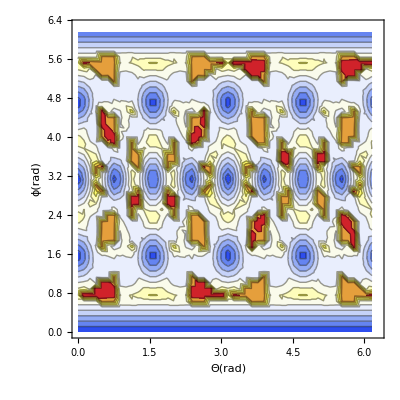

- INPUT  Database file: "/Users/lothar/Desktop/OrderParameterAnalysis/db/rotation-database_Fcc_50_1.db"

- Coordination: 12

- Number of Database items: 2500

- Number of Test item: 1

```mathematica
(* Plot distance map vs angular coordinates in a temperature scale *)
xStart=0;
xEnd=2Pi;
yStart=0;
yEnd=2*Pi;
ListContourPlot[DistMap,ColorFunction->ColorData["Temperature"],InterpolationOrder->3,Contours-> 10,ColorFunctionScaling->Automatic,PlotRange->{{xStart,xEnd},{yStart,yEnd},All},FrameLabel->{"Θ(rad)","ϕ(rad)"}]
Print["- INPUT  Database file: ",InputForm[DBfile]];
Print["- Coordination: ",coordination];
Print["- Number of Database items: ",NDBItems];
Print["- Number of Test item: ",testitem];
```

```mathematica
(* Plot of the best matching database item coordination (grey) against the testitem (red) *)
(* Both coordinations should coincide precisely *)
WhereMin=Ordering[DistMap[[All,3]],1];
DistMap[[WhereMin]];
plmodel=ListPointPlot3D[{ModelDB[[WhereMin[[1]],3]]},BoxRatios->{2,2,2},PlotRange->{{-2,2},{-2,2},{-2,2}},AxesLabel->{"X","Y","Z"},PlotStyle->Directive[Gray,PointSize[0.1],Opacity[0.5],ViewPoint->{0,0,Infinity}]];
testmodel=ListPointPlot3D[{q},BoxRatios->{2,2,2},PlotStyle->Directive[Red, PointSize[0.05],Opacity[0.5],ViewPoint->{0,0,Infinity}]];
Show[plmodel,testmodel]
```

-Graphics3D-